Created on 13 September 2021 at 13:57 by JDM (joseph.murphree@protonmail.com).

Analytic model for microwave dressing, based on the analytic model used to create the figures for the bubble paper recently submitted to the arXiv (2108.05880) (introductory_figure_analytic_small_v7.nb).

Run this notebook, then shell-thermal2-toy.nb, then the first (spin-related) portion of this document again.

```mathematica
(* Send to the right directory if necessary *)
(* the main project directory sits one above this subproject directory, i.e. at the -2 position. *)
projectDirectory=FileNameTake[NotebookDirectory[],{1,-2}]
packageDirectory=FileNameJoin@{projectDirectory,"mathematica_packages\\"}
outputDirectory=FileNameJoin@{projectDirectory,"output\\"}

If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]

Get["SMThreeChipModel.m"]
Get["SMThreeTraps.m"]
```

C:\Users\josep\forschung\modeling\bubble_bec

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

## Define fields

#### Define analytic solutions

```mathematica
evalue[m_,δ_,Ω_]:=m*hbar*Sqrt[δ^2+(Ω/2)^2];
evector[m_,δ_,Ω_]:=1./Sqrt[1+(Ω/(2*Sqrt@2))^2*((1/(δ-Abs@m*#)^2)+(1/(δ+Abs@m*#)^2))]*
{Ω/(2*Sqrt@2*(δ-Abs@m*#)),
1,
-Ω/(2*Sqrt@2*(δ+Abs@m*#))}&[evalue[m,δ,Ω]/hbar];
```

```mathematica
(*bFieldTOY[b0_,bCurve_,x_,y_,z_]:=b0+bCurve*{x^2,y^2,z^2};*)
(*bFieldMagTOY[b0_,bCurve_,x_,y_,z_]:=b0+bCurve*Sqrt[x^4+y^4+z^4];*)

anisotropy=1.0;
bFieldMagTOY[b0_,bCurve_,x_,y_,z_]:=b0+bCurve*(x^2+(y/anisotropy)^2+z^2);

b0TOY=5.*Gauss;(* G *)
omegaTrap = (2.*Pi)*20.0;(* rad/s *)
mF=1;
bCurveTOY=mRb*omegaTrap^2/(2.*mF*gF*μB );(* 1.5*10^4 *)(*T/m^2*)

(*Block[
{
k = ((gJ-gI)μB/Ahfs/h/2),
Ξ,
Field
},

Ξ[Field_]:= If[Field>= 1/k, -1,1];

ZeemanShiftLin[Field_]= {
-Ahfs-2gF μB Field/h(*+Ξ[Field]Ahfs Sqrt[1- 2k Field+k^2 Field^2]*),
-Ahfs-gF μB Field/h(*+Ahfs Sqrt[1- k Field+k^2 Field^2]*),
-Ahfs(*+Ahfs Sqrt[1+k^2 Field^2]*),
-Ahfs+ gF μB Field/h(*+Ahfs Sqrt[1+k  Field+k^2 Field^2]*),
-Ahfs+ 2 gF μB Field/h(*+ Ahfs Sqrt[1+2k  Field+k^2 Field^2]*)
} ;(* F=2, m= -2, -1, 0, +1, +2 *)

ZeemanShiftLinC = Compile[{Field},Evaluate[ZeemanShiftLin[Field]]];
];*)

(*xCor=1./Sqrt[2.]; (* was 1 *)*)

detuning[Δ_,x_,y_,z_]:=2*Pi*Δ-(μB*gF*bFieldMagTOY[b0TOY,bCurveTOY,x,y,z]/hbar); (* [rad/s] detuning from (F=1, mF)->(F=2, mF') resonance as an angular frequency *)
detuning::usage="detuning[Δ_,x_,y_,z_] takes the global detuning Δ [Hz] and the position relative to the trap center (x,y,z) [m] and returns the local detuning [rad/s] of the applied AC field from the atomic transition at that point. In the case where the AC field is in the rf range, this is simply the frequency of the field, whereas in microwave case it is the frequency of the field with the hyperfine splitting (~7 GHz) subtracted.";

adiabaticEnergiesTOY[Δ_,Ω_,x_,y_,z_]:=evalue[#,detuning[Δ,x,y,z],Ω*2*Pi]/h&/@{1,-1,0};
adiabaticEnergyStatesTOY[Δ_,Ω_,x_,y_,z_]:=evector[#,detuning[Δ,x,y,z],Ω*2*Pi]&/@{1,-1,0};
```

```mathematica
adiabaticEnergiesTOY[Δ,Ω,0,0,0]*(2*Pi)
```

{1. √((-2.19781×10^7+2 π Δ)^2+π^2 Ω^2),-1. √((-2.19781×10^7+2 π Δ)^2+π^2 Ω^2),0.}

```mathematica
Exp[-5]//N
```

0.00673795

## Plot spins

3.49253×10^6

3.53661×10^6

xMax (um) = 300.

36191.2

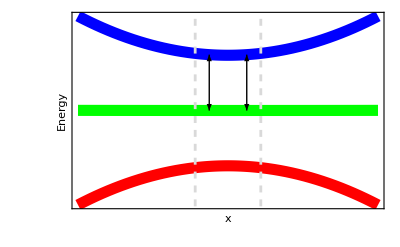

```mathematica
energySplitting=(ZeemanShift[b0TOY]//Differences)[[4]](* Hz *) (* only used in maxPotCen *)
(*cdetuning=bCurveTOY*μB*(500*10^(-6))^2/(hbar*2*Pi)*)
xPotMin=150.; (* um *) (* Set to match the population plots *)
yPotMin=anisotropy*xPotMin;(*[um]*)
cDelta=gF*μB*(b0TOY+bCurveTOY*(xPotMin*10^(-6))^2)/h
(*cDelta=(*4**)(*2**)energySplitting+50*^3; (* Hz *)*)
cOmega=(*(*Model*)(2*Pi)*)34.*1*^3; (* Hz *)
(*xPotMin=Sqrt[(hbar*2*Pi*cDelta-gF*μB*b0TOY)/(gF*μB*bCurveTOY)]*10^6;*) (* um *)
xMax= 2.*xPotMin;(* um *)
xMin=-xMax;
xStp=(xMax-xMin)/200;

Print["xMax (um) = "<>ToString@xMax];

(*
(*WORKING:*)
cDelta=(*4**)2*energySplitting+1.7*^6; (* Hz *)
cOmega=(*(*Model*)(2*Pi)*)100*1*^3; (* Hz *)
xMax=10^3; (* um *)
xMin=-xMax;
xStp=(xMax-xMin)/200;
*)

(* Evaluate the energy function on a grid in order to approximate its minimum. *)
numEnergies=Table[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]],{x,xMin,xMax,xStp}];
approxMin=Min@numEnergies;

temperature=200*10^(-9);(* [K] *)
hotVal=(*5*)-Log[0.01]*kb*temperature/h+approxMin (* Energy (in units of frequency) above which the cloud density drops to less than 1% of its maximum. *)
secLineVal=hotVal;

defaultPlotOptions=Options[Plot];

myPlotOptions={
ColorFunctionScaling->False, (* Necessary for our user-defined functions for the plots' line colors to work. *)
(* Aesthetics: *)
PlotStyle->Thickness[0.02],
PlotRange->All,
AxesOrigin->{0,0},
AxesStyle->Directive[{Thickness[0.01],Arrowheads[Automatic]}],
AxesLabel->{Automatic,"Energy"}(*,
Ticks->{{{-xPotMin,"-x_res"},{xPotMin,"x_res"}}}*),
Ticks->None,
TicksStyle->None,
Axes->False,
Frame->True,
FrameTicks->{
{0,None},
{{{-xPotMin,"-x_res"},0,{xPotMin,"x_res"}},None}}
};

myPlotOptionsNoLabels={
ColorFunctionScaling->False, (* Necessary for our user-defined functions for the plots' line colors to work. *)
(* Aesthetics: *)
PlotStyle->Thickness[0.02],
PlotRange->All,
AxesOrigin->{0,0},
AxesStyle->Directive[{Thickness[0.01],Arrowheads[Automatic]}],
AxesLabel->{Automatic,"Energy"}(*,
Ticks->{{{-xPotMin,"-x_res"},{xPotMin,"x_res"}}}*),
Ticks->None,
TicksStyle->None,
Axes->False,
Frame->True,
FrameTicks->{
{{{0,""}},None},
{{{-xPotMin,(*"-x_res"*)""},{0,""},{xPotMin,(*"x_res"*)""}},None}}
};

SetOptions[Plot,myPlotOptionsNoLabels];

Block[
{energies,
curveColors=RGBColor/@{{1,0,0},{0,1,0},{0,0,1}}(*These triplets define the RGB colors for each of the bare states, -1 (red), 0 (green), and 1 (blue), respectively.*),
plot, legend,
rangeMult=4,
arSz=0.05, (* size of arrow heads *)
lineFac=0.875
},

energies[x_]:=ZeemanShiftC[bFieldMagTOY[b0TOY,bCurveTOY,x*10^(-6),0,0]][[{1,3,5}]];

plot=Show[
Plot[energies[x][[#]],{x,rangeMult*xMin,rangeMult*xMax},
LabelStyle->{FontFamily->"Helvetica", Bold},
ColorFunction->Function[{x,y},curveColors[[#]]],
GridLines->{{lineFac*xMin,lineFac*xMax},{}},
GridLinesStyle->Directive[Dashed,Thickness[0.005]],
(* resonance arrows *)
Epilog->{
{Arrowheads[{-arSz,arSz}],Arrow[{{-xPotMin,0},{-xPotMin,energies[xPotMin][[3]]}}]},(*,
{Arrowheads[{-arSz,arSz}],Arrow[{{-xPotMin,0},{-xPotMin,energies[xPotMin][[1]]}}]}*),
{Arrowheads[{-arSz,arSz}],Arrow[{{xPotMin,0},{xPotMin,energies[xPotMin][[3]]}}]}
}(*,
PlotLabel->"Bare state energies"*)
]&/@{1,2,3}
];

legend=LineLegend[Reverse@curveColors,{"1","0","-1"}];

(*energiesBarePlot=Legended[plot,legend];*)
energiesBarePlot=plot
]
```

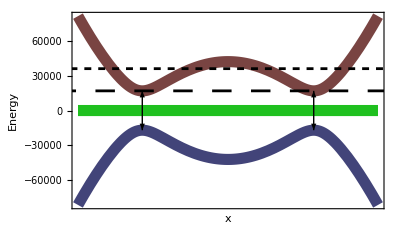

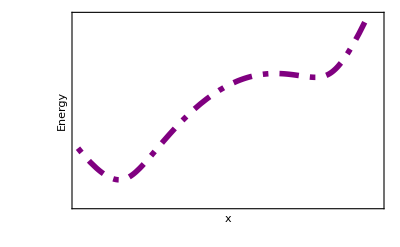

```mathematica
Block[
{energies,stateCompositionX,lineColorFunc,plot,legend,
domFac=0.875,
arSz=0.04,
minLine={Dashing[Large,None,"Round"],Thickness[0.005],Line[{{xMin,approxMin},{xMax,approxMin}}]},
hotLine={(*Dotted*)Dashing[Small,None,"Round"],Thickness[0.005],Black,Line[{{xMin,hotVal},{xMax,hotVal}}]},
maxLine={Dotted,Thickness[0.005],Line[{{xMin,secLineVal},{xMax,secLineVal}}]}},

energies[x_]:=adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0];
(* n=1 for the highest energy (and for us most interesting) eigenstate. *)
stateCompositionX[x_,n_]:=adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[n]]^2;
lineColorFunc[x_,n_]:=(RGBColor@stateCompositionX[x,n]);


plot=Show[
Plot[energies[x][[#]],{x,(*0.75**)domFac*xMin,(*0.75**)domFac*xMax},
ColorFunction->Function[{x,y},lineColorFunc[x,#]],
GridLines->{{(*0.75**)xMin,(*0.75**)xMax},{}},
GridLinesStyle->Directive[Dashed,Thickness[0.005]],
Epilog->{
{Arrowheads[{-arSz,arSz}],Arrow[{{-xPotMin,-energies[xPotMin][[1]]},{-xPotMin,energies[xPotMin][[1]]}}]},
{Arrowheads[{-arSz,arSz}],Arrow[{{xPotMin,-energies[xPotMin][[1]]},{xPotMin,energies[xPotMin][[1]]}}]},
minLine,
hotLine
},
(*PlotLabel->"Dressed state energies",*)
FrameTicks->{
{None,{{0,""},{approxMin,""},{hotVal,""}}},
{{{-xPotMin,""},{0,""},{xPotMin,""}},None}}
]&/@{1,2,3}
];

legend=LineLegend[{Blue,Green,Red},{"1","0","-1"}];

energiesDressedPlotMax=energies[domFac*xMax][[1]];

energiesDressedPlot=plot

(*Legended[plot,legend]*)
]

gravPotential[x_,gFrac_]:=gFrac*9.8*mRb*x/h;

Module[{scale=1/20,energy,offset,gFrac=0.1},
offset=-((gravPotential[#,gFrac])&[-xPotMin*10^(-6)]);
energy[x_]:=adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]];
gravPlot=Plot[
(energy[x]+gravPotential[x*10^(-6),gFrac]+offset),
{x,0.75*xMin,0.75*xMax},
PlotRange->{0,energy[xMax]},
PlotStyle->{Purple,Thickness[0.01],Dashing[{0.01,0.02,0.035,0.02},None,"Round"]},
(*ColorFunction->(colorFunc[#2]&),*)
ColorFunctionScaling->False,
Ticks->True,
PlotRange->{Automatic,energiesDressedPlotMax}]
]
```

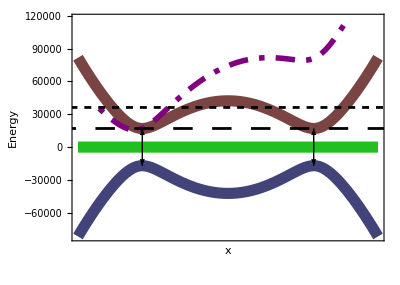

```mathematica
Show[{energiesDressedPlot,gravPlot},ImageSize->Automatic->200,BaselinePosition->Axis,AspectRatio->1/1.4]
```

-Graphics3D-

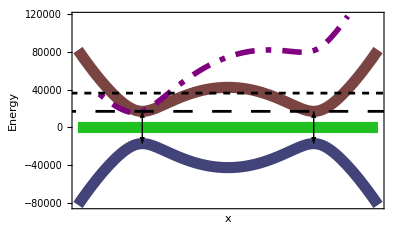
-Graphics- | -Graphics3D- | -Graphics-

```mathematica
defaultContourPlot3DOptions=Options[ContourPlot3D];
myContourPlot3DOptions={
RegionFunction->Function[{x,y,z},x<0||y>0||z<0], (* creates cross-section *)
RegionBoundaryStyle->None,
Ticks->None,
(*Boxed->False,*)
(*AxesOrigin->{0,0,0},*)
(*AxesStyle->Thickness[0.01],*)
AxesLabel->{"x","y","z"}
};

SetOptions[ContourPlot3D,myContourPlot3DOptions];

Block[{sphere,maxBound=1},
sphere[x_,y_,z_]:=x^2+y^2+z^2;

spinLegend=ContourPlot3D[
{sphere[x,y,z]==1(*,sphere[x,y,z]==3,sphere[x,y,z]==9*)},
{x,0,maxBound},{y,0,maxBound},{z,0,maxBound},
ColorFunction->Function[{x,y,z},RGBColor@{x,y,z}],
ContourStyle->Opacity[1],
Mesh->False,
BoxStyle->None,
AxesOrigin->{0,0,0},
AxesLabel->(*{"m=-1","m=0","m=1"}*)None,
Axes->True,
Boxed->False,
ViewPoint->({#,#,#}&[5]),
Lighting->{"Ambient",White},
(*PlotLabel->"Spin composition",*)
ImageSize->Tiny]
]

SetOptions[ContourPlot3D,defaultContourPlot3DOptions];

spinGrid=Grid@{{
Show[energiesBarePlot,ImageSize->Automatic->200,BaselinePosition->Axis],
spinLegend,
Show[{energiesDressedPlot,gravPlot},ImageSize->Automatic->200,BaselinePosition->Axis]}}

SetOptions[Plot,defaultPlotOptions];
```

## Plot energies

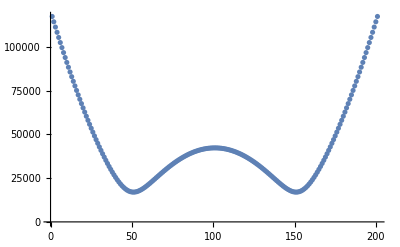

Min = -Graphics-
----------
 1000000 MHz

Max = 0.271383 MHz

Min loc = -0.000147

```mathematica
ListPlot@numEnergies

Print["Min = "<>ToString[%*10^(-6)]<>" MHz"];
plotMax=adiabaticEnergiesTOY[cDelta,cOmega,xMax*10^(-6),xMax*10^(-6),0][[1]];
Print["Max = "<>ToString[%*10^(-6)]<>" MHz"];
plotRange=(plotMax-approxMin);
(minLoc=(Ordering[numEnergies,1][[1]]*xStp-xMax)*10^(-6))//N;
Print["Min loc = "<>ToString@%];
```

```mathematica
approxMin
plotRange
colorFunc[v_]:=(ColorData["SolarColors"][1.5*(v-approxMin)/plotRange]);
colorFunc[approxMin]
colorFunc[v_]:=Module[
{f=Log@(#)&,range,min,max},
min = f[approxMin];
max=f[plotMax];
range=max-min;
Return[(ColorData["SolarColors"][(f[v]-min)/range])];
];
```

17000.

254383.

RGBColor[0.468742, 0., 0.0158236]

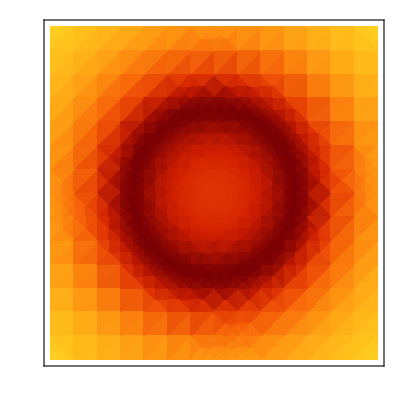

```mathematica
plotPot2d=DensityPlot[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),0][[1]],
{x,xMin,xMax},{y,xMin,xMax},
ColorFunction->(colorFunc[#1]&),
ColorFunctionScaling->False,
FrameTicks->{
{{{-yPotMin,""},{0,""},{yPotMin,""}},None},
{{{-xPotMin,""},{0,""},{xPotMin,""}},None}
}(*,
PlotLabel->"Dressed state energy contour"*)(*,
Frame->False,
Axes->True,
Ticks->False,
AxesStyle->Directive[{Thickness[0.01],Arrowheads[Automatic]}],
AxesLabel->Automatic*)(*,
MaxRecursion->4*)
]
```

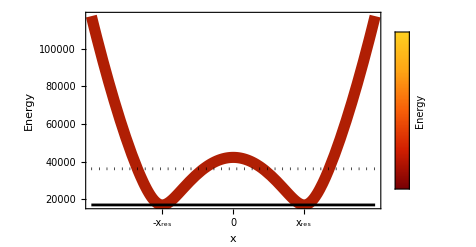

```mathematica
SetOptions[Plot,myPlotOptions];
maxPotCen=Sqrt[(cDelta-energySplitting)^2+(cOmega/2)^2];


Block[
{
minLine={Thickness[0.005],Line[{{xMin,approxMin},{xMax,approxMin}}]},
hotLine={Dashed,Thickness[0.005],Red,Line[{{xMin,hotVal},{xMax,hotVal}}]},
maxLine={Dotted,Thickness[0.005],Line[{{xMin,secLineVal},{xMax,secLineVal}}]}
},
plotPot1d=Legended[
Plot[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]],{x,xMin,xMax},
ColorFunction->(colorFunc[#2]&),
ColorFunctionScaling->False(*,
Frame->True,
Axes->False*),
Ticks->True,
Epilog->{minLine,maxLine(*,hotLine*)}],
BarLegend["SolarColors",Ticks->None,LegendLabel->"Energy"]
]
]

SetOptions[Plot,defaultPlotOptions];
```

```mathematica
NSolve[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]]==approxMin,x];
rMin=%[[3,1,2]]
NSolve[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]]==secLineVal,x];
{rIn,rOt}=Sort@%[[{2,4},1,2]]
```

150.

{62.6176,202.68}

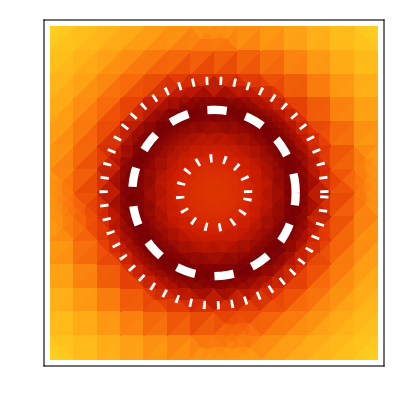

```mathematica
plotPot2dFinal=Show@{
plotPot2d,
Graphics@{White,Dashing[{0.005,0.02},None,"Round"],Thickness[0.015],Circle[{0,0},rIn],Circle[{0,0},rOt]},
Graphics@{White,Dashing[Large,None,"Round"],Thickness[0.015],Circle[{0,0},rMin]}}
```

```mathematica
(*plotPot2dContours=ContourPlot[{
adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),0][[1]]==approxMin+0.1,
adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),0][[1]]==secLineVal},
{x,xMin,xMax},{y,xMin,xMax},
(*ColorFunction->(colorFunc[#1]&),
ColorFunctionScaling->False,*)
ContourStyle->{{White,Dashed,Thickness[0.005]},{White,Dotted,Thickness[0.01]}},
Frame->False,
Axes->True,
Ticks->False,
AxesStyle->Directive[{Thickness[0.01],Arrowheads[Automatic]}],
AxesLabel->Automatic,
Mesh->All,
MaxRecursion->7
];
plotPot2dFinal=Show@{plotPot2d,plotPot2dContours}*)
```

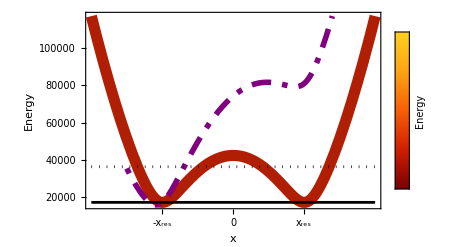

```mathematica
SetOptions[Plot,myPlotOptions];

(*Legended[
Plot[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]]+9.8*mRb*(x*10^(-6))/(2*Pi*hbar),{x,xMin,xMax},
ColorFunction->(colorFunc[#2]&),
ColorFunctionScaling->False,
Ticks->True],
BarLegend["SolarColors",Ticks->None,LegendLabel->"Energy"]
]*)



plotPot1dFinal=Show@{plotPot1d,gravPlot}

SetOptions[Plot,defaultPlotOptions];
```

```mathematica
(*Block[{energy,contourStyles,minEnergyOffset=0.15*^6,secondSurfaceOffset=5*^6},
energy[x_,y_,z_]:=(adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),z*10^(-6)][[1]]);

contourStyles=(Directive[ColorData["SolarColors"][#],Opacity[0.8]]&/@{0,1});

(*Print[contourStyles];*)

plotPot3d=ContourPlot3D[
{energy[x,y,z]==approxMin+minEnergyOffset,energy[x,y,z]==approxMin+secondSurfaceOffset},
{x,xMin,xMax},{y,xMin,xMax},{z,xMin,xMax},
(*PlotPoints->10,
MaxRecursion->4,*)
RegionFunction->Function[{x,y,z},x<0||y>0||z<0],
ContourStyle->{ColorData["SolarColors"][0],ColorData["SolarColors"][1]},
RegionBoundaryStyle->None]
]*)
```

```mathematica
(*Block[{energy,contourStyles,minEnergyOffset=0.5*^3(*,secondSurfaceOffset=5*^6*),opacity=0.2},
energy[x_,y_,z_]:=(adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),z*10^(-6)][[1]]);

contourStyles=(Directive[ColorData["SolarColors"][#],Opacity[0.8]]&/@{0,1});
Print["Min [kHz] = "<>ToString[approxMin/10^3]];
Print["Plotted min [kHz] = "<>ToString[(approxMin+minEnergyOffset)/10^3]];
Print["Seclineval [kHz] = "<>ToString[secLineVal/10^3]];
plotPot3dMin=ContourPlot3D[
energy[x,y,z]==approxMin+minEnergyOffset,
{x,xMin,xMax},{y,xMin,xMax},{z,xMin,xMax},
RegionFunction->Function[{x,y,z},(x<0||y>0||z<0)&&(x^2+(y/anisotropy)^2+z^2>((minLoc*10^6)^2))],
ContourStyle->colorFunc[approxMin],
RegionBoundaryStyle->None(*,
WorkingPrecision->20*),
MaxRecursion->1,
PlotPoints->40];

(*plotPot3dOuter=ContourPlot3D[
energy[x,y,z]==secLineVal,
{x,xMin,xMax},{y,xMin,xMax},{z,xMin,xMax},
RegionFunction->Function[{x,y,z},x<0||y>0||z<0],
ContourStyle->{colorFunc[secLineVal],Opacity[opacity]},
MeshStyle->Opacity[opacity],
RegionBoundaryStyle->None];*)

Show@{plotPot3dMin(*,plotPot3dOuter*)}

]*)
```

```mathematica
(*Block[{energy,contourStyles,opacity=0.5,minEnergyOffset=0.15*^6,secondSurfaceOffset=4*^6},
energy[x_,y_,z_]:=(adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),z*10^(-6)][[1]]);

contourStyles=(Directive[ColorData["SolarColors"][#],Opacity[0.8]]&/@{0,1});

(*Print[contourStyles];*)

plotPot3dOuter=ContourPlot3D[
energy[x,y,z]==secLineVal,
{x,xMin,xMax},{y,xMin,xMax},{z,xMin,xMax},
RegionFunction->Function[{x,y,z},x<0||y>0||z<0],
ContourStyle->{colorFunc[secLineVal],Opacity[opacity]},
MeshStyle->Opacity[opacity],
RegionBoundaryStyle->None]
]*)
```

```mathematica
(*plotPot3d=Show[plotPot3dOuter,plotPot3dMin]*)
```

```mathematica
(*energyGrid=Grid@{{
Show[plotPot1dFinal,Ticks->False],
plotPot2dFinal,
Show[plotPot3d,Ticks->False,AxesLabel->{"x","y","z"}]}};*)
```

```mathematica
(*Grid[{{spinGrid},{energyGrid},{atomGrid}},Frame->All]*)
```

Dressing a bubble in a toy spin F=1 model. The spin dependent force experienced by atoms in a quadratic magnetic field is modified by the introduction of an rf field. The potential can be derived by transforming the atomic bare state atomic Hamiltonian into a rotating frame wherein time-dependence is removed by performing the rotating wave approximation. An atom whose introduction to and movement through the resulting potential is sufficiently adiabatic remains in one of the resulting energy curves.

By detuning the rf field from resonance at the minimum of the m=1 curve, potential dips are created at the points where the field is resonant. Any straight path that passes through the origin will experience the potential dips on either side of the B field minimum. Thus the minimum of the dressed potential forms a shell in dimensions.

Atoms with sufficiently low energy will be trapped around this minimum and form a bubble-shaped cloud.

```mathematica
(*Export[FileNameJoin@{NotebookDirectory[],"fig1draft3.jpeg"},Grid[{{spinGrid},{energyGrid},{atomGrid}},Frame->All]]*)
```

## Smaller version for paper

Show::gtype: Symbol is not a type of graphics.

General::stop: Further output of Show::gtype will be suppressed during this calculation.

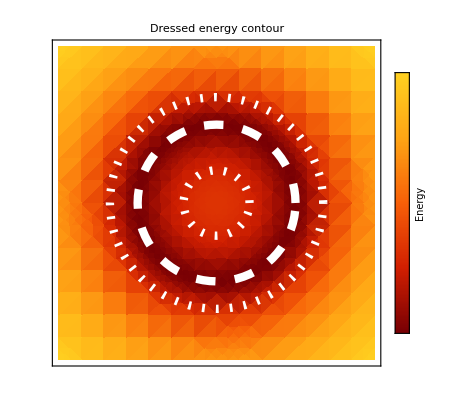
-Graphics- | -Graphics3D- | -Graphics-
-Graphics-Show[crossSectionImage,ImageSize→Automatic→150,BaselinePosition→Center,PlotLabel→Population cross-section,FrameTicks→arrayFrameTicks,FrameLabel→None]Show[absorptionImage,ImageSize→Automatic→150,BaselinePosition→Center,PlotLabel→Population, integrate z axis,FrameTicks→arrayFrameTicks,FrameLabel→None]Show[absorptionImageGravLgndls,ImageSize→Automatic→150,BaselinePosition→Center,PlotLabel→Population, w/ 5% gravity,Background→RGBColor[0.94, 0.88, 0.94]]

```mathematica
Block[
{imgSz=150,
lgdSz=100},
smallGrid=Grid@{
{spinGrid},
{
Row@{
Show[
Legended[plotPot2dFinal,Placed[BarLegend["SolarColors",Ticks->None,LegendLabel->"Energy",LegendMarkerSize->lgdSz],Left]],
ImageSize->Automatic->imgSz,BaselinePosition->Axis,PlotLabel->"Dressed energy contour"
],
Show[crossSectionImage,
ImageSize->Automatic->imgSz,BaselinePosition->Center,PlotLabel->"Population cross-section",FrameTicks->arrayFrameTicks,FrameLabel->None],

Show[absorptionImage,
ImageSize->Automatic->imgSz,BaselinePosition->Center,
PlotLabel->"Population, integrate z axis",FrameTicks->arrayFrameTicks,FrameLabel->None],

Show[
Legended[absorptionImageGravLgndls ,BarLegend["BlueGreenYellow",Ticks->None,LegendLabel->"Population",LegendMarkerSize->lgdSz]],
ImageSize->Automatic->imgSz,BaselinePosition->Center,PlotLabel->"Population, w/ 5% gravity",
Background->LightPurple]
}
}
}
]
```

```mathematica
(*Export[FileNameJoin@{NotebookDirectory[],"fig1draft1small.jpeg"},smallGrid]*)
```

```mathematica
(*SetOptions[ContourPlot3D,myContourPlot3DOptions];

Block[{sphere,plot1,plot2},
sphere[x_,y_,z_]:=x^2+y^2+z^2;
ContourPlot3D[{sphere[x,y,z]==1,sphere[x,y,z]==3,sphere[x,y,z]==9},
{x,-3,3},{y,-3,3},{z,-3,3},
(*RegionFunction->Function[{x,y,z},x<0||y>0||z<0],*)
ContourStyle->({#[1],#[0],#[1]}&[ColorData["SolarColors"]])];

plot1=ContourPlot3D[
{sphere[x,y,z]==1(*,sphere[x,y,z]==3,sphere[x,y,z]==9*)},
{x,-3,3},{y,-3,3},{z,-3,3},
RegionFunction->Function[{x,y,z},(x<0||y>0||z<0)&&(x^2+y^2+z^2<1.1)],
ContourStyle->(colorFunc[#1]&)(*({#[1],#[0],#[1]}&[ColorData["SolarColors"]])*)];

plot2=ContourPlot3D[{(*sphere[x,y,z]==1,*)sphere[x,y,z]==9(*,sphere[x,y,z]==9*)},
{x,-3,3},{y,-3,3},{z,-3,3},
ContourStyle->{Opacity[0.2],(colorFunc[#1]&)}(*({#[1],#[0],#[1]}&[ColorData["SolarColors"]])*),
MeshStyle->{Opacity[0.2]}];

Show@{plot1,plot2}

]

SetOptions[ContourPlot3D,defaultContourPlot3DOptions];*)
```

```mathematica
(*
Plot[adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]]^2,{x,xMin,xMax}]
Plot[Total@(#^2)&[adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]]],{x,xMin,xMax}]*)
```

```mathematica
(*Options[ContourPlot3D]*)
```

```mathematica
(*SetOptions[Plot,myPlotOptions];*)

(*Block[
{energies,stateCompositionX,lineColorFunc,plot,legend,range=cOmega,xMin=xMin,xMax=xMax},

energies[x_]:=adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0];
(* n=1 for the highest energy (and for us most interesting) eigenstate. *)
stateCompositionX[x_,n_]:=adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[n]]^2;
lineColorFunc[x_,n_]:=(RGBColor@stateCompositionX[x,n]);

plot=Show[
Plot[energies[x][[#]],{x,xMin,xMax},PlotRange->{-range,range},AxesOrigin->Automatic,
ColorFunction->Function[{x,y},lineColorFunc[x,#]],
Epilog->{{Dashed,Line[{{xMin,0.5*cOmega},{xMax,0.5*cOmega}}]},
{Dashed,Line[{{xMin,-0.5*cOmega},{xMax,-0.5*cOmega}}]}}]&
/@{1,2,3}
];

legend=LineLegend[{Blue,Green,Red},{"1","0","-1"}];

energiesDressedPlot=plot;

Legended[plot,legend];
]

Show[energiesDressedPlot]

SetOptions[Plot,defaultPlotOptions];*)
(* Dashed line is Rabi freq/2 (cOmega/2) *)
```

```mathematica
(*SetOptions[Plot,myPlotOptions];
(*cDelta=energySplitting+200*^3;*)
Block[
{energies,stateCompositionX,lineColorFunc,plot,legend,xMax=535,xMin},
xMin=-xMax;

energies[x_]:=adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0];
(* n=1 for the highest energy (and for us most interesting) eigenstate. *)
stateCompositionX[x_,n_]:=adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[n]]^2;
lineColorFunc[x_,n_]:=(RGBColor@stateCompositionX[x,n]);

plot=Show[
Plot[energies[x][[#]],{x,xMin,xMax},
ColorFunction->Function[{x,y},lineColorFunc[x,#]],
Ticks->Automatic,PlotRange->All]&
/@{1,2,3}
];

legend=LineLegend[{Blue,Green,Red},{"1","0","-1"}];

energiesDressedPlot=plot;

Legended[plot,legend];
]

Show@energiesDressedPlot
(*Sqrt[hbar*cDelta*2*Pi/(2*mRb*omegaTrap^2)]*10^6*)
Sqrt[hbar*cDelta*2*Pi/(bCurveTOY*μB)]*10^6
SetOptions[Plot,defaultPlotOptions];*)
```

```mathematica
(*analyticPotential[Delta_,Omega_,x_,y_,z_]:=Module[
{r=Sqrt[x^2+y^2+z^2],fL0,fLr,fPot},
(*fL0=((ZeemanShiftC[b0TOY]//Differences)[[4]]//N);*)
fLr:=ZeemanShiftC[bFieldMagTOY[b0TOY,bCurveTOY,x,y,z]][[4]];
fPot=Sqrt[(cDelta(*+fL0*)-fLr)^2+(Omega/2)^2];
Return[fPot];
];

SetOptions[Plot,myPlotOptions];
(*cDelta=energySplitting+200*^3;*)
Block[
{energies,stateCompositionX,lineColorFunc,plot,legend,xMax=xMax,xMin},
xMin=-xMax;

energies[x_]:=adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0];
(* n=1 for the highest energy (and for us most interesting) eigenstate. *)
stateCompositionX[x_,n_]:=adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[n]]^2;
lineColorFunc[x_,n_]:=(RGBColor@stateCompositionX[x,n]);

plot=Show[
Plot[energies[x][[#]],{x,xMin,xMax},
ColorFunction->Function[{x,y},lineColorFunc[x,#]],
Ticks->Automatic,PlotRange->All]&
/@{1}
];

legend=LineLegend[{Blue,Green,Red},{"1","0","-1"}];

energiesDressedPlot=plot;
analyticPlot=Plot[analyticPotential[cDelta,cOmega,x*10^(-6),0,0],{x,xMin,xMax}];

Legended[plot,legend];
]

Show[energiesDressedPlot, analyticPlot,PlotRange->All]


SetOptions[Plot,defaultPlotOptions];*)
```